```mathematica
connectOneBarabasiAlbert[g_Graph/;ConnectedGraphQ[g]]:=g;
connectOneBarabasiAlbert[g_Graph]:=Module[{cmps=ConnectedComponents[g],pos},
pos=Flatten[Intersection[Position[VertexInDegree[seed],0],Select[cmps,Length[#]==Min[Length/@cmps]&]]];
If[pos=={},g,
EdgeAdd[g,RandomChoice[{1,2,3}]->RandomChoice[pos]]
]
]
```

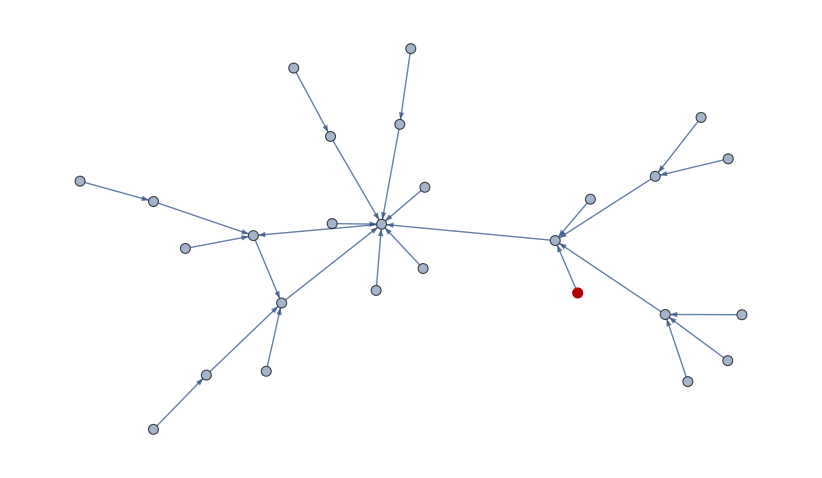

```mathematica
HighlightGraph[seed,27]
```

```mathematica
ConnectedComponents[seed]
```

{{1,2,3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

```mathematica
Position[VertexInDegree[seed],0]
```

{{5},{10},{12},{13},{14},{15},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

```mathematica
Length/@ConnectedComponents[seed]
```

{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Min[Length/@ConnectedComponents[seed]]
```

1

```mathematica
Select[ConnectedComponents[seed],Length[#]==Min[Length/@ConnectedComponents[seed]]&]
```

{{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

```mathematica
Intersection[Position[VertexInDegree[seed],0],Select[ConnectedComponents[seed],Length[#]==Min[Length/@ConnectedComponents[seed]]&]]
```

{{5},{10},{12},{13},{14},{15},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

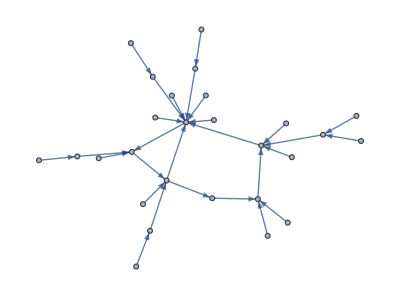

```mathematica
EdgeAdd[seed,RandomChoice[{1,2,3}]->RandomChoice[Flatten[Intersection[Position[VertexInDegree[seed],0],Select[ConnectedComponents[seed],Length[#]==Min[Length/@ConnectedComponents[seed]]&]]]]]
```

```mathematica
ConnectedComponents[%]
```

{{1,2,3,6,9,10},{4},{5},{7},{8},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

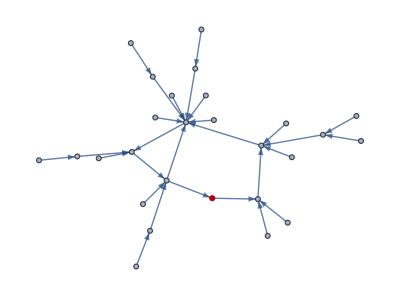

```mathematica
HighlightGraph[%%,10]
```

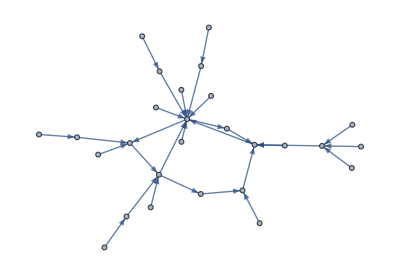

```mathematica
EdgeAdd[%%%,RandomChoice[{1,2,3}]->26]
```

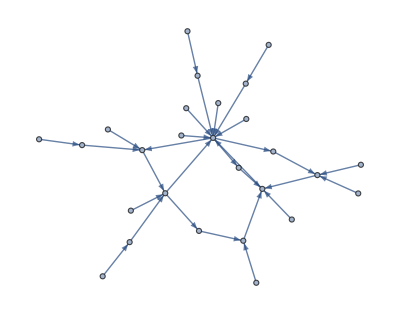

```mathematica
EdgeAdd[%,RandomChoice[{1,2,3}]->25]
```

```mathematica
ConnectedComponents[%]
```

{{1,2,3,6,9,16,25,26,27},{4},{5},{7},{8},{10},{11},{12},{13},{14},{15},{17},{18},{19},{20},{21},{22},{23},{24}}

```mathematica
tst={{0,1,1,1,1},{0,0,1,1,0},{0,1,0,1,1},{1,1,0,0,0},{0,0,0,1,0}};
```

```mathematica
tst=AdjacencyGraph[tst]
```

-Graphics-

```mathematica
Partition[Range[10],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
graph=graphToNet[tst,Partition[Range[10],2]]
```

{{{1,2},{2,3,4,5}},{{3,4},{3,4,5}},{{5,6},{2,4}},{{7,8},{1,3}},{{9,10},{4}}}

```mathematica
M=Length[graph]
```

5

```mathematica
rem=remove[graph,Range[Length[graph]]]
```

{{1,3},{2,5},{3,4},{4,1},{5,4}}

```mathematica
add[graph,%]
```

{{{},{1}},{{},{3}},{{1},{5}},{{5,9},{}},{{3},{9}}}

```mathematica
graph
```

{{{1,2},{2,3,4,5}},{{3,4},{3,4,5}},{{5,6},{2,4}},{{7,8},{1,3}},{{9,10},{4}}}

```mathematica
packs=graph[[All,1]]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
Table[Drop[packs[[i]],Length[%39[[i,2]]]],{i,M}]
```

{{2},{4},{6},{7,8},{10}}

```mathematica
Table[Flatten[Append[%44[[i]],%39[[i,1]]]],{i,M}]
```

{{2},{4},{6,1},{7,8,5,9},{10,3}}

```mathematica
Transpose[{%46,graph[[All,2]]}]
```

{{{2},{2,3,4,5}},{{4},{3,4,5}},{{6,1},{2,4}},{{7,8,5,9},{1,3}},{{10,3},{4}}}